# Mathematica III - Linear Algebra

## Based on Labs developed by John S. Colton, BYU Physics & Astronomy, based in part on past labs by Branton Cambell and Steve Turley

In most fields of science and engineering, the easiest multi-variable problems are the "linear" ones, where the unknown quantities appear in linear combinations with constant coefficients.  Linear problems are usually solved by straightforward methods and have exact solutions.  Non-linear problems, on the other hand, can become very difficult very quickly.  In this lab, we will explore matrix and vector properties and operations, practice formulating problems in terms of matrix/vector equations, and learn how to use Mathematica's linear-algebra capabilities to solve simple and moderately-challenging math and physics problems.

```mathematica
Clear["`*" ]
```

## Lists & vectors

Lists are Mathematica objects that are items grouped together with curly brackets. A list can be any collection of items: numbers, unassigned variables, plots, even other lists.  You' ve already used them in a few ways--to specify limits in the Plot command, to apply a list of rules inside functions, and to evaluate functions with variables set to particular values.  In addition to their utility in evaluating functions, the three primary purposes of lists are to (1) serve as “arrays” for programming purposes, (2) allow you to do linear algebra with vectors and matrices, and (3) allow you to manipulate real data.  We’ll focus on #2 here.

### How to create a list.

There are numerous ways to create lists in Mathematica. Look over these examples and press F1 on the function names if it’s not clear what’s going on.

```mathematica
list = {1,2,3,4,5}
```

```mathematica
list^2
```

```mathematica
list2={a,b,c,d,e}
```

```mathematica
list2^2
```

```mathematica
(#^2 &) @list   (* nameless function to operate on list elements, prefix form *)
```

```mathematica
Range[10]
```

```mathematica
Range[10,20]
```

```mathematica
range = Range[0,10,.2]    (* general format for Range:  start, end, step size *)
```

```mathematica
(#^2 &) @ range
```

```mathematica
Table[n^2, {n,3,7}]
```

```mathematica
Table[n^2, {n,1,5,0.1}]    (* general format for Table: start, end, step size  *)
```

```mathematica
f[x_] = x^3;
Array[f, 10]
```

```mathematica
Array[#^3&,10]
```

Things to observe: There are lots of ways to construct lists! The five ways used here are:
1. Manually defining a list with curly brackets.
2. Operating on an existing list
3. The Range command, to create an equally-spaced set of “points” (list elements)
4. The Table command, as a very flexible way of creating a set of function values
5. The Array command, as a slightly less flexible way of doing the same (with some added capability to create multi-dimensional lists)

### “Regular vectors” are lists

Here’s an example of a vector

```mathematica
vec={1,2,3}
```

## Defining matrices

### Typing in matrix elements and viewing matrices in standard form

A matrix is a list of lists.  Each of the sub-lists is a list of row elements.  One way to enter them is to type them in directly.

```mathematica
matx1={{1,2,3},{4,5,7},{8,9,10}} 
matx2={{11},{12},{13}}
matx3={{14, 15, 16}}
```

You can view them in standard matrix form using MatrixForm:

```mathematica
MatrixForm[matx1]
matx2//MatrixForm  (*using postfix notation - often easier!*)
matx3//MatrixForm
```

The MatrixForm command works on regular vectors too:

```mathematica
vec
vec//MatrixForm
```

IMPORTANT: Be careful that, when you define matrices (or vectors), you do not include MatrixForm in the definition - just use it after the definition to view them.  For example:

```mathematica
incorrect={{a,b},{c,d}}   //MatrixForm  (* this will produce bad results *)
incorrect //Det  (* The determinant function fails to work *)

correct={{a,b},{c,d}}  
% //MatrixForm  
correct //Det (* this works! *)
```

The “incorrect” example doesn’t work because the formatting statement MatrixForm has been included as part of the definition, which prevents it from behaving as a matrix.

### Two ways to use templates to enter matrices

You can also use templates to insert matrices.  
Method #1:  From the toolbar at the top of the screen, choose Palettes, Basic Math Assistant.  Under “Basic Commands” open the matrix tab: 
 -Graphics-
Here you’ll find a matrix template, and lots of typical matrix commands.

Method #2: In addition, you can insert matrices using Insert...Table/Matrix from the toolbar at the top of the screen: -Graphics-

There are lots of other ways to generate matrices - from data, from functions, etc.  See the tutorial howto/CreateAMatrix

### Problem 1: Matrices three ways

a) Create three 3x2 matrices (3 rows, 2 columns) and name them M1, M2, and M3 in the following ways: 
 (1) Create M1 by typing in entries directly as a list of lists.  
 (2) Use the Palette to create M2.  
 (3) Use Insert...Table/Matrix to create M3.  Use whatever values you like but make each matrix different.  Make use of these keyboard shortcuts:

For the template-created matrices, use the keyboard commands
	Tab or arrow	to move through the empty placeholders
	Ctrl-Enter	to enter a new row immediately below the cursor
	Ctrl-,		to enter a new column to the right of the cursor
	Ctrl-Space	to move out of the matrix
You can also start a new matrix simply by typing Ctr-Enter or Ctrl-,

b) Enter each matrix name to evaluate it and verify that it is a list of lists, regardless of the entry method

c) On another line use MatrixForm to view each matrix in standard format

### 1D matrices vs “regular” vectors

It may seem like one-dimensional matrices are the same as vectors, but that’s not quite true.  Evaluate the examples below, which contain a “regular vector” v, and the 3x1 and 1x3 matrices A and B, respectively. Elements like A and B are often called “column vectors” and “row vectors”, but Mathematica treats them a little differently than just “regular vectors” such as {1,2,3}. Specifically, these column and row vectors are 2D matrices whereas a regular vector is a 1D list of three elements, and you don’t have to specify whether it is a row or column vector. Most of the time Mathematica will figure out how to handle a “regular vector” as shown in the multiplication examples which follow.

```mathematica
v={1,2,3}; (* regular vector *)
A = {{4},{5},{6}};  (* 3x1 column matrix *)
B = {{7,8,9}};  (* 1x3 row matrix *)
matx4={{a,b,c},{d,e,f}}; (* a 2x3 matrix to test out the vectors on *)
matx5={{a,b},{c,d},{e,f}}; (* a 3x2 matrix to test out the vectors on *)
MatrixForm/@{v,A,B,matx4,matx5} (* the command MatrixForm "mapped" onto A, B, v, and matx4 *)
```

```mathematica
matx4.v//MatrixForm (* the product ({{a, b, c}, {d, e, f}})({{1}, {2}, {3}}) Mathematica treats the vector v as a column vector*)
matx4.A//MatrixForm(* the product ({{a, b, c}, {d, e, f}})({{4}, {5}, {6}}) *)
matx4.B//MatrixForm (* the product ({{a, b, c}, {d, e, f}})({{7, 8, 9}}) which does NOT work *)
```

```mathematica
v.matx5//MatrixForm (* the product ({{1, 2, 3}})({{a, b}, {c, d}, {e, f}}) Mathematica treats the vector v as a row vector*)
A.matx5//MatrixForm(* the product ({{4}, {5}, {6}})({{a, b}, {c, d}, {e, f}}) which does NOT work *)
B.matx5//MatrixForm (* the product ({{7, 8, 9}})({{a, b}, {c, d}, {e, f}}) *)
```

### How to access individual matrix elements / vector components

Mathematica uses double square brackets to indicate specific list elements. (This is technically a shortcut for the Part function.) For example:

```mathematica
vec={1,2,3}
vec[[3]]
```

```mathematica
vec[3] (*wrong way!)
```

Things to observe:
1. If you accidentally try to access a list element using single square brackets instead of double, Mathematica will be very confused. In the example labeled “wrong way”, it thinks that you want to evaluate the vec function at x=3. But no such function exists, so it is unable to comply with the request and spits out a garbage answer. Be very careful to use double square brackets to refer to list items.

Elements of a matrix
You can refer to an individual matrix element just as you would an element of a list of lists.  There are actually two ways of doing this. Look at the output of these two commands:

```mathematica
matx1={{1,2,3},{4,5,7},{8,9,10}} ;
%//MatrixForm
```

```mathematica
matx1[[2]]             (* [[2]] picks out the second of the three lists of row elements in matx1 *)
matx1[[2]][[3]]  (* [[2]][[3]] then takes that row list and returns the 3rd element.  *)
```

Here’s the alternative, which is a little less awkward-looking:

```mathematica
matx1[[2,3]]
```

Much nicer, and in keeping with standard matrix notation

### Problem 2: Matrix elements

The command Eigensystem[M] finds the eigenvalues and eigenvectors of matrix M.  (More on this in a bit).  Here’s what the output looks like:

```mathematica
M={{1,3},{2,2}};
M//MatrixForm
Eigensystem[M]
Eigensystem[M]//MatrixForm  (* easier to see what this matrix looks like if you put it in standard form *)
```

The two elements (4 and -1) in the first row are the two eigenvalues of M.  The two vectors {1,1} and {-3,2} in the second row are the eigenvectors associated with each of the eigenvalues.

a) Use the Part function (double brackets [[ ]]) to pull out the second eigenvalue (i.e. -1) from the matrix returned by Eigensystem[M]
b) Use double brackets to pull out the second eigenvector (i.e. {-3,2}) from the matrix returned by Eigensystem[M] 
c) Use double brackets to pull out the first element (i.e. -3) of the second eigenvector.  Hint: There are several ways to do this, including an extension of the “alternative” method described above.  See if you can do this with just ONE set of double-brackets

### Matrix multiplication, dot product

Mathematica's matrix multiplication operation is called Dot (shortcut ".").  This is the same operator used for vector dot products. 

In order for two matrices to be multipliable, the number of columns in the first matrix must equal the number of rows in the second matrix.  If, for example, A is an m×n matrix and B is an n×p matrix, then A.B will be an m×p matrix.

```mathematica
A= {{1,2},{3,4},{5,6}};  (* a 3x2 matrix *)
% //MatrixForm
B = {{8,7,6,5},{4,3,2,1}};  (* a 2x4 matrix *)
%//MatrixForm
A.B //MatrixForm  (* a 3x4 matrix *)  (* also, it's OK to do MaxtrixForm like this here there's no new matrix being defined at the same time. If you wanted to define C=A.B, then you couldn't use the //MatrixForm bit on the same line *)
B.A // MatrixForm  (* doesn't work; wrong dimensions *)
```

Element-wise operations: Watch out for * instead of . mistakes!!
It’s easy to forget you need to use “.” when multiplying matrices.  If the matrices don’t have the same dimensions this will lead to an error message:

```mathematica
A.B//MatrixForm
A*B//MatrixForm
```

But if the matrices have the same dimensions you can get into trouble.  Consider this example:

```mathematica
F={{1,2},{3,4}};
% //MatrixForm
G = {{8,7},{6,5}};
% //MatrixForm
```

```mathematica
F.G//MatrixForm
F*G//MatrixForm  (* incorrect format for matrix multiplication *)
```

You can see that when you use “*” mathematica multiplies individual matrix elements together rather than mutiiplying the matrices themselves together.  Be alert to this!
Other operations which work in this way on individual elements: +, -, ^
These are efficient ways to manipulate matrices if you are aware of what they are doing

Here’s an example of the vector dot product.

```mathematica
v1={1,2,3}
v2={3,4,5}
v1.v2  (* the dot product *)
v2.v1 (* the dot product again *)
```

Things to notice: this is another example of the way Mathematica treats a “regular vector” - a simple list - differently from a 1D column or row matrix (for which order definitely matters)

### Matrix and vector manipulation

Mathematica contains all of the vector and matrix manipulation functions you would expect to find.  Some of the most useful are:
Matrices
	Transpose[m]			transpose m^ᵀ
	ConjugateTranspose[m]	conjugate transpose m^† (Hermitian conjugate)
	Inverse[m]			matrix inverse
	Det[m]				determinant
	Minors[m]			matrix of minors
	Minors[m,k]			k^th minors
	Tr[m]				trace
	MatrixRank[m]		rank of matrix
	Eigenvectors[m]		list of eigenvectors
	Eigenvalues[m]		list of eigenvalues (not necessarily in same order as eigenvectors)
	Eigensystem[m]		eigenvectors & their associated eigenvalues
	RowReduce[m]		the row reduced form of m
Vectors
	Dot (.)				dot product.  Use a period for the dot.
	Cross (×) 			cross product.  Enter using Esc cross Esc
	Norm[v]			gives the norm of a vector (its length), complex number (its absolute value), or matrix
	Div[v], Grad[v], Curl[v]	the divergence, gradient, curl
	Normalize[v]			the unit vector in the direction of v

### Problem 3: Determinants

(3.3.2 from HW#7) Find the determinant of:
	(5 | 17 | 3
2 | 4 | −3
11 | 0 | 2)

### Inverting matrices to solve systems of linear equations

A vitally important application of matrices is to solve systems of linear equations. For example, consider these simulataneous equations: 
2x + 2y + 3z = 4
3x + 4y - 5z = 6
2x - 2y + z = 1

They can be written in this equivalent matrix form:
Mr = k
(2 | 2 | 3
3 | 4 | -5
2 | -2 | 1)(x
y
z)=(4
6
1)

Written in matrix form, and with a nice program such as Mathematica around to do the matrix inversion, the solution is easily obtained by multiplying both sides by the inverse of the matrix: 
M^-1 Mr = M^-1 k
r = M^-1 k
(x
y
z) = Inverse(2 | 2 | 3
3 | 4 | -5
2 | -2 | 1) .  (4
6
1)

```mathematica
M = {{2,2,3},{3,4,-5},{2,-2,1}};
M //MatrixForm
k = {4,6,1};  (* using a regular vector instead of a 3x1 column vector *)
k //MatrixForm
```

```mathematica
r=Inverse[M]. k ;
r //MatrixForm //N  (* show r in standard form, evaluate numerically 8)
```

Notice: In Mathematica the inverse of a matrix M is *not* M^-1.  It’s Inverse[M] 

The solution to the three simultaneous equations above is x = 1.175, y = 0.7125, and z = 0.075.  In this particular case, the Solve command also could have been used to solve the system of equations, but the technique of inverting matrices to solve systems of equations is very generally applicable and one you should know.

#### Problem 4: matrix inversion

(3.2.12 from HW 7)  a) Set up the following set of simultaneous equations in the form M.r = k, and solve for r (i.e. the vector whose components are the values of x, y, and z) using matrix inversion as in the example above. b) check your answer by multiplying the matrix M by the vector r and formatting using MatrixForm to see that it gives you k.
	2x + 5y + 1 = 2
	x + y + 2z = 1
	x + 5z = 3

## Eigenvalues and eigenvectors

The functions Eigenvalues and Eigenvectors give you the eigenvalues and eigenvectors of a matrix. That is, they give you the only possible numbers and vectors which are solutions of the “eigenvalue equation”  M.r = λ r, where λ is a number, r is a generalized “vector” (i.e. not necessarily representing 3D space), and M is the matrix. The matrix must be square. There are the same number of eigenvalues and eigenvectors as there are rows (or columns) of the matrix, although some eigenvalues could be repeated. The solutions are sometimes written as λ_1, λ_2, λ_3, ..., and r_1, r_2, r_3, ..., meaning that M.r_1=λ_1r_1  and so forth. 

The command Eigenvalues outputs a list containing the allowed values of the constant λ. 

The command Eigenvectors outputs a matrix in which each ROW contains the allowed values of the vector r. Eigenvectors are only defined up to a multiplicative constant. That is, if you have a 2x2 matrix where (1,3) is an eigenvector, then Mathematica might report (1,3) for the eigenvector... or (2,6), or even (1/sqrt(10), 3/sqrt(10)). They are all equivalent.

Each eigenvalue has a particular eigenvector associated with it. Unfortunately, Mathematica doesn’t always sort the eigenvectors returned by the Eigenvectors command in the same order that the eigenvalues are given in results of the Eigenvalues command. The additional function called Eigensystem allows you to see which ones correspond to which.

#### Problem 5: Eigenvectors & eigenvalues

(3.11.15 from HW 7)  a) Define the following matrix, then display it in standard form:  M=(2 | 3 | 0
3 | 2 | 0
0 | 0 | 1)
b) Find the eigenvalues and eigenvectors of M using the commands Eigenvalues and Eigenvectors.  Display the output of each, then see what it looks like in standard form using MatrixForm as well.
c) Use double brackets after the Eigenvectors command to pick out the second of the three eigenvectors.  Check to see that you did this correctly - the second eigenvector is the second row of the matrix output by the Eigenvectors command
d) Find the eigenvalues and eigenvectors of M using the command Eigensystem.  On another line, display the output in standard form.
e) Use double brackets to pick out the second eigenvalue from the Eigensystem command, and use double brackets to pick out its associated eigenvector.

### Coupled harmonic oscillators: normal modes

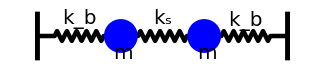
Here is an example that may help you understand what eigenvalues and eigenvectors represent and why they are useful in physics.

The following system of two masses and three springs is an example of coupled harmonic oscillators. The masses happen to be equal and two of the springs happen to have the same spring constant, but that wouldn’t necessarily need to be the case.

-Graphics-

Before we solve this system, let’s review the simpler problem of a single mass connected to a single spring - the simple harmonic oscillator.  Using  Newton’s Second Law: F_net=m a, the only force acting on the mass is from the spring;  the equation becomes:

m(d^2 x)/dt^2=-k x

For this you might guess a solution of the form x=A cos(ωt), or perhaps x=A_ sin(ωt), depending on whether it starts with some displacement or at equilibrium. Plugging that trial solution into the equation, it’s easy to show that the equation is true as long as ω=√(k/m). Problem solved!

Back to coupled masses & springs. If the middle spring were not present the two masses would each oscillate at ω=√(k_b/m). However, the middle spring couples the oscillations, and (as you will see) there are now two different fundamental modes of oscillation at two different frequencies.

To analyze the coupled system, we’ll do it like the SHO and start with Newton’s Second Law--but applied to each mass individually. Let’s call “u” the displacement of the left mass and “v” the displacement of the right mass. The net displacement of the center spring is then v-u. Each spring supplies a force according to Hooke’s Law, F_spring=kΔx. Here are the two equations, with signs chosen very carefully so that the springs push/pull in the right directions:

m(d^2 u)/dt^2=k_s(v-u)-k_b u
m(d^2 v)/dt^2=-k_bv-k_s(v-u)

Grouping terms a little differently:

m(d^2 u)/dt^2=u(-k_b-k_s) + v(k_s)
m(d^2 v)/dt^2=u(k_s)+v(-k_b-k_s)

Since a single mass on a spring oscillates sinusoidally, let’s make a guess and assume that each mass here will just oscillate back and forth in a sinusoidal fashion, both of them at the same ω and each with a constant amplitude (not necessarily the same). This assumption turns out to NOT be true in general, as you will see in the next section. But it is true if the starting positions of the masses are chosen carefully. The oscillation modes for which this assumption is true are called the “normal modes” of the system. 

With this assumption, the displacements u and v will then have solutions of the form u=u_0 cos(ωt) and v=v_0 cos(ωt), where u_0 and v_0 are the amplitudes of oscillation. As with solving the SHO, the next thing to do is to plug those guesses into the equations and see under what conditions the equations can be true.

The time derivative on the left hand side of the top equation becomes: d^2/dt^2(u_0 cosωt) =-ω^2 u_0 cos(ωt), and the time derivative for the bottom equation is -ω^2 v_0 cos(ωt). Multiplying by -1 and dividing by cos(ωt), the simultaneous equations now simplify to:

m ω^2 u_0=u_0(k_b+k_s) + v_0(-k_s)
m ω^2 v_0=u_0(-k_s)+v_0(k_b+k_s)

Or, in matrix form, with λ=m ω^2:

λ(u_0
v_0) = (k_b+k_s | -k_s
-k_s | k_b+k_s)(u_0
v_0)

This is now an eigenvalue equation:  M.r = λ r , where λ is a constant, r is a two element “vector”, and M is a matrix. Not just any λ and r can work! In fact, in this case only two λ’s will yield solutions to the equation. (Remember there are the same number of eigenvalues as there are simultaneous equations.) Finding the eigenvalues will tell you what the allowed oscillation frequencies are: one allowed ω for each λ (because ω=√(λ/m)). 

Each eigenvalue & frequency will also have a particular r (eigenvector) associated with it. In this example r = (u_0,v_0)... that means the eigenvectors give you information about the initial displacements of each mass that will give rise to the allowed frequencies. As mentioned above, eigenvectors can always be multiplied by a constant, so if a particular (u,v) combination “works”, then any constant times that (u,v) pair will also work and will produce the same λ--so the eigenvectors really only tell you about the ratios of the amplitudes, not about their absolute values. As an example, this means that if you get (1,3) as an eigenvector, then for that mode of oscillation the second mass would always have three times the amplitude of the first mass. It wouldn’t matter if the amplitudes of oscillation were 1 cm vs. 3 cm, 2 cm vs. 6 cm, etc., all such amplitudes will give rise to the same frequency. Or, if you get (-1,3) as an eigenvector, then that means the oscillations are out of phase: the ratio of amplitudes is still 3 to 1, but one starts out displaced to the left of its equilibrium point while the other is displaced to the right.

Enough discussion, let’s solve the problem already!

### Problem 6. Coupled harmonic oscillators, normal modes

For simplicity, let's set m = 1 and k_s=k_b=1 for some choice of units. 
a) Create the matrix M of spring constants and the vector r containing the initial positions u_0 and v_0.
b) Use Mathematica to solve the eigenvalue equation and determine what two frequencies are allowed, along with what the relationship is between u_0 and v_0 for each allowed frequency. 
c) Compare the two frequencies of the two modes to the frequency the masses would have if they were not coupled together. Qualitatively explain why the allowed frequencies are higher, lower, or the same as the uncoupled case.

By the way, notice how easily this approach could straight-forwardly be applied to a MUCH larger system of coupled masses and springs. You just have to be able to specify the appropriate “spring constant matrix”.  The answer to that problem turns out to be very closely connected to the allowed vibrational modes in a solid (you can think of the masses as being vibrating atoms and the springs as being the bonds between the atoms).

### Plotting the positions as a function of time

If you set up the matrix M correctly above, then the oscillation frequencies omega1 and omega2 corresponding to the two normal modes are:

```mathematica
omega1=Sqrt[Eigensystem[M][[1,1]]/m]/.m->1
omega2=Sqrt[Eigensystem[M][[1,2]]/m]/.m->1
```

The initial positions u0 and v0 of the two masses for each of the two normal modes are given by the eigenvectors.  Let’s call these uinit1 & vinit1 for the first mode, and uinit2 & vinit2 for the second mode.

```mathematica
uinit1=Eigensystem[M][[2,1,1]]
vinit1=Eigensystem[M][[2,1,2]]
uinit2=Eigensystem[M][[2,2,1]]
vinit2=Eigensystem[M][[2,2,2]]
```

Finally, add in the time dependence cos[ωt] for each to get the time-dependent positions of the masses for each normal mode:

```mathematica
upos1[t_]=uinit1*Cos[omega1*t]
vpos1[t_]=vinit1*Cos[omega1*t]
upos2[t_]=uinit2*Cos[omega2*t]
vpos2[t_]=vinit2*Cos[omega2*t]
```

### Problem 7. Coupled harmonic oscillators, plots

a) Plot the positions of the masses as a function of time for the first normal mode.  Plot them both on the same graph.
b) Repeat for normal mode 2

### Problem 8. Coupled harmonic oscillators, general solution

If you shook this oscillator to get it moving it probably would NOT oscillate in a normal mode.  So what good are they?  The normal modes of oscillation are important because they serve as “basis functions” from which you can build ANY general oscillation.  As a simple example, let’s construct an oscillation by adding together equal amounts of the two normal modes - so the oscillation will be 1/2 mode 1 + 1/2 mode 2.  Then for example the position of mass 1 will be 1/2 upos1[t]+1/2 upos2[t].  
a) Make a plot of the two masses undergoing this type of vibration
b) Does the oscillation pattern repeat itself?  Do the two masses have the same oscillation frequencies?

### Animations

A little animation goes a long way in helping you visualize the normal modes.  You do that with a combination of Animate and Graphics.  Here is an example of each:

```mathematica
Graphics[{Thick,Green,Line[{{0,0},{3,0}}],Blue,Ball[{1.5,0},.15]}]
```

```mathematica
Animate[Graphics[{Thick,Green,Line[{{0,0},{3,0}}],Blue,Ball[{1.5+upos1[t],0},.15]},PlotRange->All],{t,0,10}]
```

Things to notice:
- All of the Graphics elements are collected together into a list and enclosed in {curly brackets}.
- Items are plotted in the order in which they are called.  Try switching Blue and Green in one of the Graphics calls above.
Try altering some of the other graphics parameters to see if they behave as you would expect
There are many other options you can add to these commands.  Put your cursor on Animate and press F1 to see some examples

Important:  Animate is fussy - it wants to see all of the time-dependent functions directly inside the Animate call.  So THIS doesn’t work, even though it seems like it should behave exactly the same as the call above:

```mathematica
testposn=upos1[t]; (* This doesn't work inside the Animate command *)
Animate[Graphics[{Thick,Green,Line[{{0,0},{3,0}}],Blue,Ball[{1.5+testposn,0},.15]},PlotRange->All],{t,0,10}]
```

Back to the problem: For this problem we want to show the strings stretching in time, attached to the balls which move in time.  We’ll set this inside a frame containing the outer walls, and some tickmarks which show the equilibrium points.  

To start a complicated Animate command like this, break it down into managable parts which you can debug then combine together. 
I’ll start with the piece “wallgraphics” which contains the info needed to plot the walls & equilibrium points.  

Through trial and error I found that good values to use for the equilibrium positions of the two masses (i.e. the places where u=0 and v=0) are at -1.5 and +1.5, and that a good position for the walls that the springs are attached to are -3.5 and +3.5.  I made the walls extend from y = - 0.5 to +0.5, and the equilibrium markers extend from y = - 0.1 to + 0.1.  Nothing sacred about these values!

```mathematica
x0=1.5 (* equilib positions of the masses are at ±x0 *);
xwall=3.5 (* wall positions are at ±xwall *);
wallgraphics={Thick,Black,Line[{{-xwall,-.5},{-xwall,.5}}],Line[{{xwall,-.5},{xwall,.5}}],Thin,Line[{{-x0,-.1},{-x0,.1}}],Line[{{x0,-.1},{x0,.1}}]};
```

Nothing to see if you just call it:

```mathematica
wallgraphics
```

The way to see what it holds is to insert it into the Graphics command:

```mathematica
Graphics[wallgraphics]
```

Now we want to animate the balls & springs.  You do this by assembling another Graphics call which tells Mathematica where the spring endpoints are (using Line), where the balls are located and what their size is (using Ball), then placing that inside an Animate command.  Here’s what that looks like for the first ball & spring oscillating in the first normal mode:

```mathematica
Animate[Graphics[{Thick,Blue,Line[{{-xwall,0},{-x0+upos1[t],0}}],Ball[{-x0+upos1[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

Once you have everything as you wish, put it together under a single Animate call:

```mathematica
Animate[Graphics[{wallgraphics,Thick,Blue,Line[{{-xwall,0},{-x0+upos1[t],0}}],Ball[{-x0+upos1[t],0},.15]},PlotRange->{{-xwall,xwall},{-1,1}}],{t,0,50},AnimationRate->2]
```

### Problem 9. Coupled harmonic oscillators, animation

a) Modify the animation above to include the second oscillating mass and the other two springs.  Give them all different colors.  Mathematica recognizes color names such as Blue, Yellow, Red, Green, Magenta, Brown, Black, White, and others.  Mathematica draws the object in the order you list them, so you may have to play around with the order in which you call them to get them placed properly in front of or behind other objects.

b) When you have finished (a), copy & paste the animation command to another line, then modify it so that it shows the second normal mode.

What to turn in
When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#10-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 9).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.